```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
f={#1,Around[#2,#3]}&;
```

```mathematica
data1=Import["Pythia/Tests/delta_phi_1e7_1014_1420_2641_2641_10_100_dps.csv"];
data2=Import["Pythia/Tests/delta_phi_1e7_1014_1420_2641_2641_10_250_dps.csv"];
data3=Import["Pythia/Tests/delta_phi_1e7_1014_1420_2641_2641_10_500_dps.csv"];
data4=Import["Pythia/Tests/delta_phi_1e7_1014_1420_2641_2641_10_1000_dps.csv"];
data5=Import["Pythia/Tests/delta_phi_1e7_1014_1420_2641_2641_10_2000_dps.csv"];
data6=Import["Pythia/Tests/delta_phi_1e7_1014_1420_2641_2641_10_10000_dps.csv"];
data7=Import["Pythia/Tests/delta_phi_1e7_1014_1420_2641_2641_10_1000000_dps.csv"];data8=Import["Pythia/Tests/delta_phi_1e7_1014_1420_2641_2641_mpi.csv"];
```

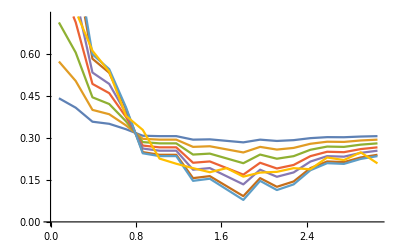

```mathematica
plot1=ListPlot[{data1,data2,data3,data4,data5,data6,data7,data8},PlotLegends->MaTeX/@{"\\sigma_{\\text{eff}}=10","\\sigma_{\\text{eff}}=25","\\sigma_{\\text{eff}}=50","\\sigma_{\\text{eff}}=100","\\sigma_{\\text{eff}}=200","\\sigma_{\\text{eff}}=1000","\\sigma_{\\text{eff}}=100000","\\text{MPI}"},Joined->True]
```

```mathematica
Export["dps1.pdf",plot1]
```

dps1.pdf

```mathematica
datapp=Import["Pythia/STAR7/delta_phi_1e7_1014_1420_2641_2641_250_dps_pp.csv"];
dataAu=Import["Pythia/STAR7/delta_phi_1e7_1014_1420_2641_2641_250_dps_Au.csv"];
dataAl=Import["Pythia/STAR7/delta_phi_1e7_1014_1420_2641_2641_250_dps_Al.csv"];
```

```mathematica
dataAu2=Import["Pythia/STAR7/delta_phi_1e7_1014_1420_2641_2641_250_dps_Au_2.csv"];
dataAl2=Import["Pythia/STAR7/delta_phi_1e7_1014_1420_2641_2641_250_dps_Al_2.csv"];
```

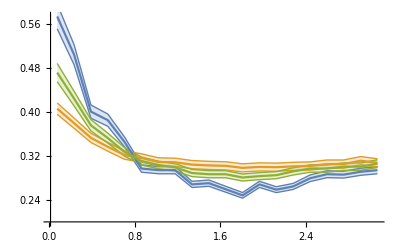

```mathematica
plot2=ListPlot[{f@@@datapp,f@@@dataAu,f@@@dataAl},PlotLegends->MaTeX/@{"p+p","p+\\mathrm{Au}","p+\\mathrm{Al}"},PlotRange->{All,{0.2,All}},Joined->True,IntervalMarkers->"Bands"]
```

```mathematica
Export["dps5.pdf",plot2]
```

dps5.pdf

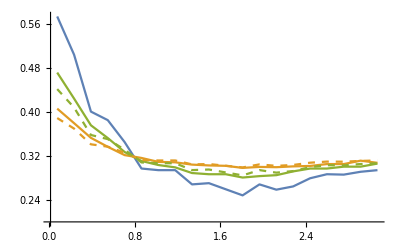

```mathematica
plot3=ListPlot[{f@@@datapp,f@@@dataAu,f@@@dataAl,f@@@dataAu2,f@@@dataAl2},PlotLegends->MaTeX/@{"p+p","p+\\mathrm{Au} \\ \\text{(nPDF)}","p+\\mathrm{Al} \\ \\text{(nPDF)}","p+\\mathrm{Au}","p+\\mathrm{Al}"},PlotRange->{All,{0.2,All}},Joined->True,IntervalMarkers->None,PlotStyle->{Automatic,Automatic,Automatic,{Dashed,ColorData[97,"ColorList"][[2]]},{Dashed,ColorData[97,"ColorList"][[3]]}}]
```

```mathematica
Export["dps6.pdf",plot3]
```

dps6.pdf